```mathematica
另一个例子:脉冲相关
```

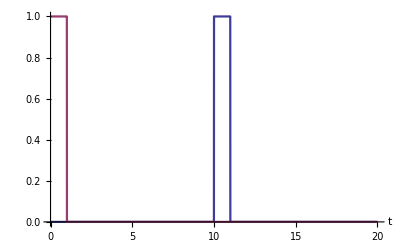

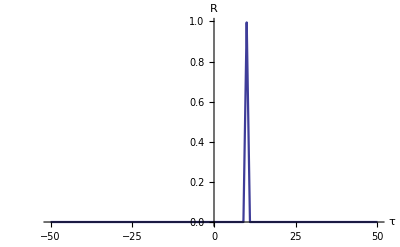

```mathematica
x[t_]:=HeavisideTheta[(t-10)*(11-t)];
g[t_]:=HeavisideTheta[t*(1-t)];tm=50.0;
Plot[{x[t],g[t]},{t,0,20},
AxesLabel->{"t",None},
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004],
BaseStyle->{FontSize->13}]
y[τ_]:=Integrate[x[t]*g[t-τ],{t,0,tm}]
Plot[Evaluate[y[t1]],{t1,-tm,tm},
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004],
AxesLabel->{"τ","R"},
BaseStyle->{FontSize->13}]
Clear[x,y,g,tm]
```